```mathematica
rmanga[x_]:=x+(1/alpha)*Log[1+Exp[-alpha*x]];
rx=rmult/rp+g;
yx=Evaluate[rmanga[rx]];
eq=rp*yx-rmult==0;
Solve[eq,rmult]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rmult→(-alpha g rp-rp Log[-1+ⅇ^(-alpha g)])/alpha}}

```mathematica
rmanga2[x_]:=x+(1/alpha)*(-x*alpha+Log[1+Exp[alpha*x]]);
rx=rmult/rp+g;
yx=Evaluate[rmanga[rx]];
eq2=rp*yx-rmult==0;Solve[eq2,rmult];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Solve[eq2,rmult]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rmult→(-alpha g rp-rp Log[-1+ⅇ^(-alpha g)])/alpha}}

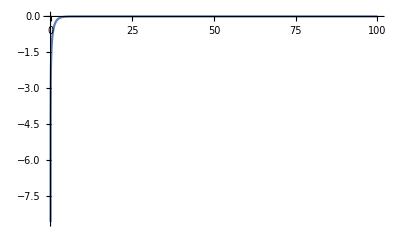

```mathematica
alpha=1;
rp=1;
Plot[(-alpha g rp+rp Log[-1+ⅇ^(alpha g)])/alpha,{g,-100,100},PlotRange->All]
```

1/x

1/x^2

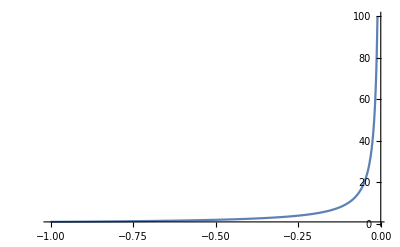

```mathematica
g=D[Log[x],x]
dg=-D[g,x]
Plot[-1/x,{x,-1,-0.01},PlotRange->All]
```